```mathematica
Exit[]
```

#### Utilities & Colors

```mathematica
Comb1={RGBColor["#206a5d"],RGBColor["#81b214"],RGBColor["#ffcc29"],RGBColor["#f58634"]};
Comb2={RGBColor["#d92027"],RGBColor["#ff9234"],RGBColor["#ffcd3c"],RGBColor["#35d0ba"]};
Comb3={RGBColor["#252525"],RGBColor["#6930c3"],RGBColor["#64dfdf"],RGBColor["#80ffdb"]};
Comb4={RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#40a8c4"],RGBColor["#a2d5f2"]};
Comb5={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
Comb6={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"Palatino"],α Degree],Scaled[{x,y}]]
```

## 3rd order WKB approximation (generic halo)

```mathematica
path=SetDirectory[NotebookDirectory[]];
SetDirectory[path];
<<HaloFlux`
```

```mathematica
MBH=1; (*Black hole mass*)
l=2; (*angular number of perturbation*)
s=2;
n=Table[i,{i,0,4}];(*overtone number n=0 is the fundamental mode*)
```

```mathematica
QNM=List[];
```

```mathematica
g[r_]=(1-2m[r]/r);
```

```mathematica
V[r_]:=-f[r]((l(l+1))/r^2+(2(1-s^2) m[r])/r^3-(1-s)m'[r]/r^2);
```

```mathematica
drdrs[r_]:=Sqrt[f[r]*g[r]]
```

```mathematica
(*functions needed for the 3rd order WKB*)
V1=drdrs[r]*D[V[r],r]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V2=Simplify[drdrs[r]* D[V1,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V3=Simplify[drdrs[r]* D[V2,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V4=Simplify[drdrs[r]*D[V3,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V5=Simplify[drdrs[r]*D[V4,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V6=Simplify[drdrs[r]*D[V5,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
```

## WKB evaluation

```mathematica
(*The WKB formula up to 3rd order of expansion in the effective potential*)
V0=ω^2+V[r];
α=Table[n[[i]]+1/2,{i,1,5}];P=Table[1/(2*V2)^(1/2)*(1/8*V4/V2*(1/4+α[[i]]^2)-1/288*(V3/V2)^2*(7+60*α[[i]]^2)),{i,1,5}];Ω=Table[α[[i]]/(2*V2)*(5/6912*(V3/V2)^4*(77+188*α[[i]]^2)-1/384*V3^2*V4/V2^3*(51+100*α[[i]]^2)+1/2304*(V4/V2)^2*(67+68*α[[i]]^2)+1/288*V3*V5/V2^2*(19+28*α[[i]]^2)-1/288*V6/V2*(5+4*α[[i]]^2)),{i,1,5}];c1=Table[I*V0/(2*V2)^(1/2)-I*P[[i]]-Ω[[i]],{i,1,5}];
For[i=1,i<6,i++,omega=FindRoot[c1[[i]]-α[[i]],{ω,0.1-0.09*I}];(*the guess here is completely random and the mode is still correct because it is the closest solution to the problem.*)
Clear[r];
Clear[ω];
ω=ω/.omega[[1]];Print[ω];AppendTo[QNM,ω];ω>>>"z=0.000001.dat";
Clear[ω];];
```

0.373162-0.0892174 ⅈ

0.346017-0.274915 ⅈ

0.302935-0.471064 ⅈ

0.247462-0.672897 ⅈ

0.178753-0.878674 ⅈ

```mathematica
QNM
```

{0.373162-0.0892174 ⅈ,0.346017-0.274915 ⅈ,0.302935-0.471064 ⅈ,0.247462-0.672897 ⅈ,0.178753-0.878674 ⅈ}

```mathematica
REAL=Table[Re[QNM[[i]]],{i,1,5}]
IM=Table[-Im[QNM[[i]]],{i,1,5}]
```

{0.373162,0.346017,0.302935,0.247462,0.178753}

{0.0892174,0.274915,0.471064,0.672897,0.878674}

```mathematica
REAL>>>"z=0.000001.dat"
IM>>>"z=0.000001.dat"
```

## Hern

```mathematica
path=SetDirectory[NotebookDirectory[]];
SetDirectory[path];
<<HaloFlux`
```

```mathematica
δω[z_,l_,s_]:=Block[{mbh=1,M,a0,ρmetric,f,m,g,drdrs,rh,r,ω,V,V1,V2,V3,V4,V5,V6,radii, V0,α,P,Ω,c1, omega},
g[r_]=(1-2m[r]/r);V[r_]:=-f[r]((l(l+1))/r^2+(2(1-s^2) m[r])/r^3-(1-s)m'[r]/r^2);drdrs[r_]:=Sqrt[f[r]*g[r]];
(*functions needed for the 3rd order WKB*)
V1=drdrs[r]*D[V[r],r]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V2=Simplify[drdrs[r]* D[V1,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V3=Simplify[drdrs[r]* D[V2,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V4=Simplify[drdrs[r]*D[V3,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V5=Simplify[drdrs[r]*D[V4,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V6=Simplify[drdrs[r]*D[V5,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
rh=2mbh;
a0=72;
M=a0 z;

ρmetric=background["HQ",M,a0,10^5][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

radii=FindRoot[V1==0,{r,3}];
(*Set r as the light ring radius by copying the radius right after the event horizon*)
(*rapprox=3 MBH(1+M MBH/a0^2);*)
Clear[r];
r=r/.radii;

(*The WKB formula up to 3rd order of expansion in the effective potential*)
V0=ω^2+V[r];
α=1/2;P=1/(2*V2)^(1/2)*(1/8*V4/V2*(1/4+α^2)-1/288*(V3/V2)^2*(7+60*α^2));Ω=α/(2*V2)*(5/6912*(V3/V2)^4*(77+188*α^2)-1/384*V3^2*V4/V2^3*(51+100*α^2)+1/2304*(V4/V2)^2*(67+68*α^2)+1/288*V3*V5/V2^2*(19+28*α^2)-1/288*V6/V2*(5+4*α^2));c1=I*V0/(2*V2)^(1/2)-I*P-Ω;
omega=FindRoot[c1-α,{ω,0.1-0.09*I}];(*the guess here is completely random and the mode is still correct because it is the closest solution to the problem.*)
Clear[r];
Clear[ω];
ω=ω/.omega[[1]];
PrintTemporary[ω];
(*{z,ω}>>>"WKB.dat";*)
Return[{z,Re[ω],Im[ω]}]
]
```

```mathematica
compactness=Range[-6,-2,1/4]
```

{-6,-23/4,-11/2,-21/4,-5,-19/4,-9/2,-17/4,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2}

```mathematica
WKBl2Vac=δω[0,2,2];
```

```mathematica
WKBl3Vac=δω[0,3,2];
```

```mathematica
WKBl4Vac=δω[0,4,2];
```

```mathematica
WKBl2=Monitor[Table[δω[10^compactness[[ii]],2,2],{ii,1,Length[compactness]}],ii];
```

```mathematica
WKBl3=Monitor[Table[δω[10^compactness[[ii]],3,2],{ii,1,Length[compactness]}],ii];
```

```mathematica
WKBl4=Monitor[Table[δω[10^compactness[[ii]],4,2],{ii,1,Length[compactness]}],ii];
```

```mathematica
datal2HT=Join[{WKBl2Vac},WKBl2];
datal3HT=Join[{WKBl3Vac},WKBl3];
datal4HT=Join[{WKBl4Vac},WKBl4];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
(*datal2HT[[All,2]]>>>"WKB.dat";
-datal2HT[[All,3]]>>>"WKB.dat";
datal3HT[[All,2]]>>>"WKB.dat";
-datal3HT[[All,3]]>>>"WKB.dat";
datal4HT[[All,2]]>>>"WKB.dat";
-datal4HT[[All,3]]>>>"WKB.dat";*)
```

```mathematica
line0R=Fit[datasetR[datal2HT,10^-2],{x,x^2},x]
```

0.955297 x-0.141567 x^2

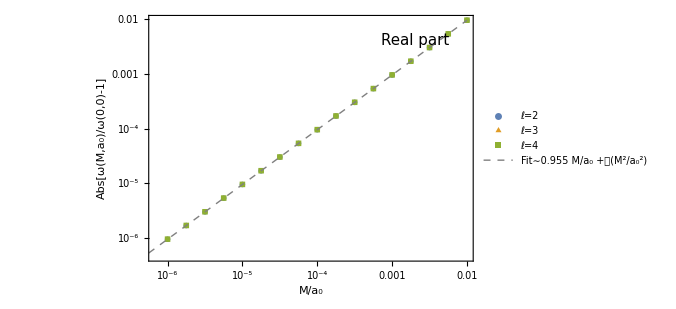

./plot/realZ_Hern_WKB.pdf

```mathematica
Show[ListLogLogPlot[{
datasetR[datal2HT,10^-2],
datasetR[datal3HT,10^-2],
datasetR[datal4HT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.82,0.9,Black]}],LogLogPlot[line0R,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.955 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_Hern_WKB.pdf",%]
```

```mathematica
line0I=Fit[datasetI[datal2HT,10^-2],{x,x^2},x]
```

0.995348 x-0.177371 x^2

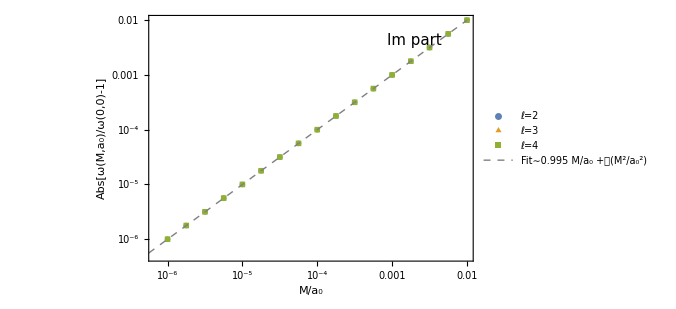

./plot/imZ_Hern_WKB.pdf

```mathematica
Show[ListLogLogPlot[{
datasetI[datal2HT,10^-2],
datasetI[datal3HT,10^-2],
datasetI[datal4HT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.82,0.9,Black]}],LogLogPlot[line0I,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.995 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_Hern_WKB.pdf",%]
```

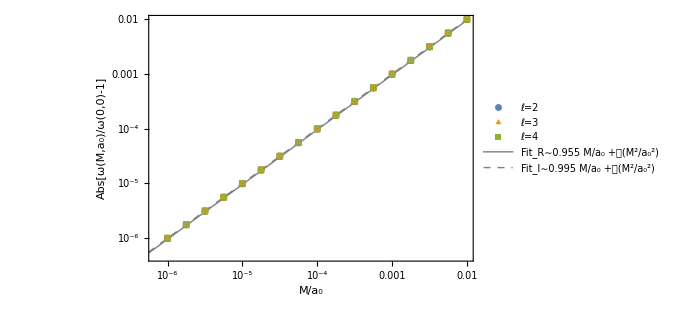

./plot/allZ_Hern_WKB.pdf

```mathematica
Show[ListLogLogPlot[{
datasetR[datal2HT,10^-2],
datasetR[datal3HT,10^-2],
datasetR[datal4HT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}}],LogLogPlot[{line0R,line0I},{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,AbsoluteThickness[1]],Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.955 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼0.995 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]],ListLogLogPlot[{
datasetI[datal2HT,10^-2],
datasetI[datal3HT,10^-2],
datasetI[datal4HT,10^-2]},Frame->True,PlotMarkers->{{○,Large},{△,Medium},{□,Small}}]]
Export["./plot/allZ_Hern_WKB.pdf",%]
```

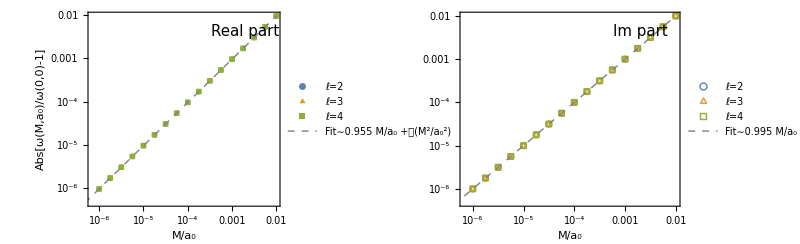

./plot/side_Z_Hern_WKB.pdf.pdf

```mathematica
p1=Show[ListLogLogPlot[{
datasetR[datal2HT,10^-2],
datasetR[datal3HT,10^-2],
datasetR[datal4HT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.82,0.9,Black]}],LogLogPlot[line0R,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.955 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]];

p2=Show[ListLogLogPlot[{
datasetI[datal2HT,10^-2],
datasetI[datal3HT,10^-2],
datasetI[datal4HT,10^-2]},Frame->True,FrameLabel->{{None,None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{○,Large},{△,Medium},{□,Small}},
Epilog->{leg["Im part",15,0,0.82,0.9,Black]}],LogLogPlot[line0I,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.995 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]];
GraphicsRow[{p1,p2},ImageSize->Full,Spacings->Scaled[0]]
Export["./plot/side_Z_Hern_WKB.pdf.pdf",%]
```

```mathematica
Export["WKB_Hern.m",{datal2HT,datal3HT, datal4HT}]
```

WWKB_Hern.m

## NFW

```mathematica
path=SetDirectory[NotebookDirectory[]];
SetDirectory[path];
<<HaloFlux`
```

```mathematica
δωN[z_,l_,s_]:=Block[{mbh=1,M,a0,rc,ρmetric,f,m,g,drdrs,rh,r,ω,V,V1,V2,V3,V4,V5,V6,radii, V0,α,P,Ω,c1, omega},
g[r_]=(1-2m[r]/r);V[r_]:=-f[r]((l(l+1))/r^2+(2(1-s^2) m[r])/r^3-(1-s)m'[r]/r^2);drdrs[r_]:=Sqrt[f[r]*g[r]];
(*functions needed for the 3rd order WKB*)
V1=drdrs[r]*D[V[r],r]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V2=Simplify[drdrs[r]* D[V1,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V3=Simplify[drdrs[r]* D[V2,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V4=Simplify[drdrs[r]*D[V3,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V5=Simplify[drdrs[r]*D[V4,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
V6=Simplify[drdrs[r]*D[V5,r]]//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify;
rh=2mbh;
a0=536;
M=a0 z;
rc=5*a0;

ρmetric=background["NFW",M,{a0,rc},10^5][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

radii=FindRoot[V1==0,{r,3}];
(*Set r as the light ring radius by copying the radius right after the event horizon*)
(*rapprox=3 MBH(1+M MBH/a0^2);*)
Clear[r];
r=r/.radii;

(*The WKB formula up to 3rd order of expansion in the effective potential*)
V0=ω^2+V[r];
α=1/2;P=1/(2*V2)^(1/2)*(1/8*V4/V2*(1/4+α^2)-1/288*(V3/V2)^2*(7+60*α^2));Ω=α/(2*V2)*(5/6912*(V3/V2)^4*(77+188*α^2)-1/384*V3^2*V4/V2^3*(51+100*α^2)+1/2304*(V4/V2)^2*(67+68*α^2)+1/288*V3*V5/V2^2*(19+28*α^2)-1/288*V6/V2*(5+4*α^2));c1=I*V0/(2*V2)^(1/2)-I*P-Ω;
omega=FindRoot[c1-α,{ω,0.1-0.09*I}];(*the guess here is completely random and the mode is still correct because it is the closest solution to the problem.*)
Clear[r];
Clear[ω];
ω=ω/.omega[[1]];
PrintTemporary[ω];
(*{z,ω}>>>"WKB_NFW.dat";*)
Return[{z,Re[ω],Im[ω]}]
]
```

```mathematica
compactness=Range[-6,-2,1/4]
```

{-6,-23/4,-11/2,-21/4,-5,-19/4,-9/2,-17/4,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2}

```mathematica
WKBl2VacN=δωN[0,2,2];
```

```mathematica
WKBl3VacN=δωN[0,3,2];
```

```mathematica
WKBl4VacN=δωN[0,4,2];
```

```mathematica
WKBl2N=Monitor[Table[δωN[10^compactness[[ii]],2,2],{ii,1,Length[compactness]}],ii];
```

```mathematica
WKBl3N=Monitor[Table[δωN[10^compactness[[ii]],3,2],{ii,1,Length[compactness]}],ii];
```

```mathematica
WKBl4N=Monitor[Table[δωN[10^compactness[[ii]],4,2],{ii,1,Length[compactness]}],ii];
```

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

```mathematica
datal2NT=Join[{WKBl2VacN},WKBl2N];
datal3NT=Join[{WKBl3VacN},WKBl3N];
datal4NT=Join[{WKBl4VacN},WKBl4N];
```

```mathematica
(*Join[{WKBl2VacN[[2]]},WKBl2N[[All,2]]]>>>"WKB_NFW.dat";
Join[{-WKBl2VacN[[3]]},-WKBl2N[[All,3]]]>>>"WKB_NFW.dat";
Join[{WKBl3VacN[[2]]},WKBl3N[[All,2]]]>>>"WKB_NFW.dat";
Join[{-WKBl3VacN[[3]]},-WKBl3N[[All,3]]]>>>"WKB_NFW.dat";
Join[{WKBl4VacN[[2]]},WKBl4N[[All,2]]]>>>"WKB_NFW.dat";
Join[{-WKBl4VacN[[3]]},-WKBl4N[[All,3]]]>>>"WKB_NFW.dat";*)
```

```mathematica
line0RN=Fit[datasetR[datal2NT,10^-2],{x,x^2},x]
```

0.867096 x-0.10841 x^2

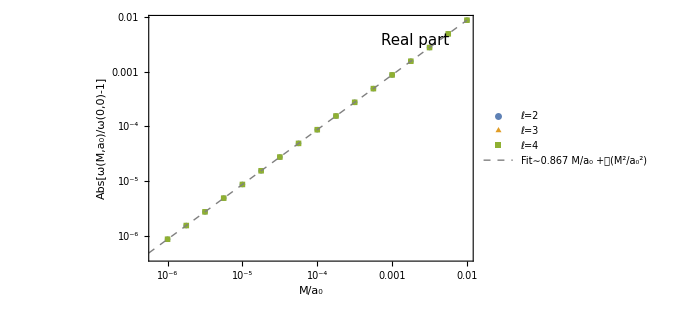

./plot/realZ_NFW_WKB.pdf

```mathematica
Show[ListLogLogPlot[{
datasetR[datal2NT,10^-2],
datasetR[datal3NT,10^-2],
datasetR[datal4NT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.82,0.9,Black]}],LogLogPlot[line0RN,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.867 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/realZ_NFW_WKB.pdf",%]
```

```mathematica
line0IN=Fit[datasetI[datal2NT,10^-2],{x,x^2},x]
```

0.870196 x-0.111079 x^2

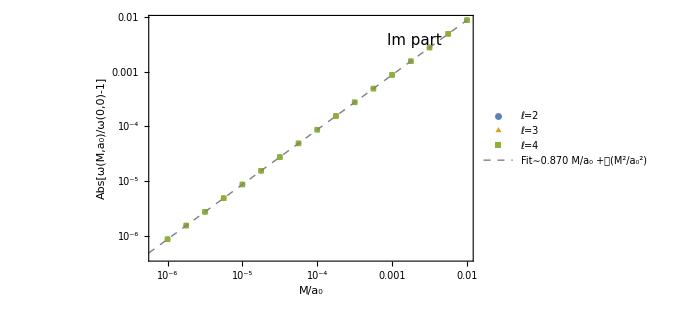

./plot/imZ_NFW_WKB.pdf

```mathematica
Show[ListLogLogPlot[{
datasetI[datal2NT,10^-2],
datasetI[datal3NT,10^-2],
datasetI[datal4NT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Im part",15,0,0.82,0.9,Black]}],LogLogPlot[line0IN,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.870 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]]
Export["./plot/imZ_NFW_WKB.pdf",%]
```

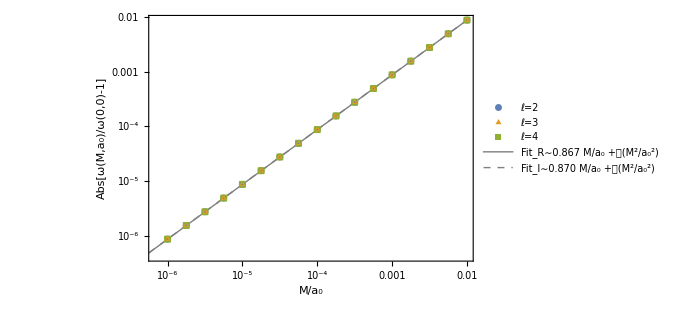

./plot/allZ_NFW_WKB.pdf

```mathematica
Show[ListLogLogPlot[{
datasetR[datal2NT,10^-2],
datasetR[datal3NT,10^-2],
datasetR[datal4NT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}}],LogLogPlot[{line0RN,line0IN},{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,AbsoluteThickness[1]],Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit_R∼0.867 M/a_0 +𝒪(M^2/a_0^2)",13],Style["Fit_I∼0.870 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]],ListLogLogPlot[{
datasetI[datal2NT,10^-2],
datasetI[datal3NT,10^-2],
datasetI[datal4NT,10^-2]},Frame->True,PlotMarkers->{{○,Large},{△,Medium},{□,Small}}]]
Export["./plot/allZ_NFW_WKB.pdf",%]
```

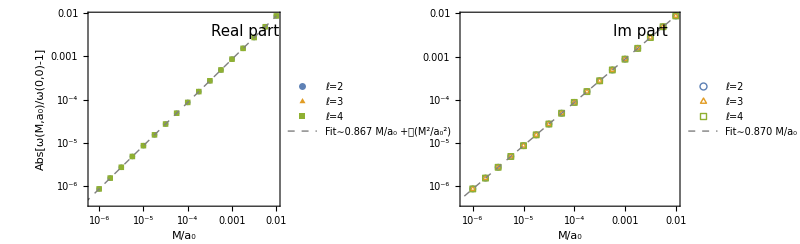

./plot/side_Z_NFW_WKB.pdf.pdf

```mathematica
p1=Show[ListLogLogPlot[{
datasetR[datal2NT,10^-2],
datasetR[datal3NT,10^-2],
datasetR[datal4NT,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",15],None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{●,Large},{▲,Medium},{■,Small}},
Epilog->{leg["Real part",15,0,0.82,0.9,Black]}],LogLogPlot[line0RN,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.867 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]];

p2=Show[ListLogLogPlot[{
datasetI[datal2NT,10^-2],
datasetI[datal3NT,10^-2],
datasetI[datal4NT,10^-2]},Frame->True,FrameLabel->{{None,None},{Style["M/a_0",15],None}},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",12,FontFamily->"Palatino"],Style["ℓ=3",12,FontFamily->"Palatino"],Style["ℓ=4",12,FontFamily->"Palatino"]},Scaled[{0.1,0.75}]],ImageSize->500,ImagePadding->{{70, 50}, {60, 10}},PlotMarkers->{{○,Large},{△,Medium},{□,Small}},
Epilog->{leg["Im part",15,0,0.82,0.9,Black]}],LogLogPlot[line0IN,{x,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Gray,Dashed,AbsoluteThickness[1]]},PlotLegends->Placed[{Style["Fit∼0.870 M/a_0 +𝒪(M^2/a_0^2)",13]},Scaled[{0.7,0.25}]]]];

GraphicsRow[{p1,p2},ImageSize->Full,Spacings->Scaled[0]]
Export["./plot/side_Z_NFW_WKB.pdf.pdf",%]
```

```mathematica
Export["WKB_NFW.m",{datal2NT,datal3NT, datal4NT}]
```

WKB_NFW.m

## Old requests

```mathematica
ωReal=List[0.3736715982,0.3467109239,0.3010534085,0.2515058439]
```

{0.373672,0.346711,0.301053,0.251506}

```mathematica
ωWKBappR= List[0.37316197949698093,0.3460171857304088,0.3029346170124718,0.24746189087773446]
```

{0.373162,0.346017,0.302935,0.247462}

```mathematica
ωIm=List[0.0889622840,0.2739147749,0.4782767840,0.7051374430]
```

{0.0889623,0.273915,0.478277,0.705137}

```mathematica
ωWKBappI= List[0.08921741557246682,0.27491525436357306,0.4710638240926919,0.6728974598749307]
```

{0.0892174,0.274915,0.471064,0.672897}

```mathematica
(ωWKBappR- ωReal)/ωReal
```

{-0.00136381,-0.00200091,0.00624875,-0.016079}